# 向量

## 鸢尾花数据集

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];(*导入Iris数据集*)
```

```mathematica
RandomSample[irisData,10]//TableForm
```

{5.5,2.3,4.,1.3}→versicolor
{6.5,3.,5.8,2.2}→virginica
{5.8,4.,1.2,0.2}→setosa
{6.3,3.4,5.6,2.4}→virginica
{6.2,2.2,4.5,1.5}→versicolor
{7.3,2.9,6.3,1.8}→virginica
{5.4,3.9,1.3,0.4}→setosa
{4.9,3.1,1.5,0.2}→setosa
{5.4,3.7,1.5,0.2}→setosa
{6.6,2.9,4.6,1.3}→versicolor

## 概率密度估计

```mathematica
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];(*花萼长宽花瓣长宽写成数组*)
```

```mathematica
{Mean[#],StandardDeviation[#]}&/@{sepalLength,sepalWidth,petalLength,petalWidth}(*计算均值和标准差*)
```

{{5.84333,0.828066},{3.05733,0.435866},{3.758,1.7653},{1.19933,0.762238}}

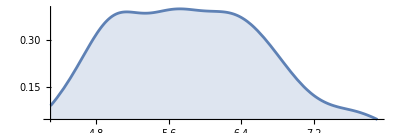
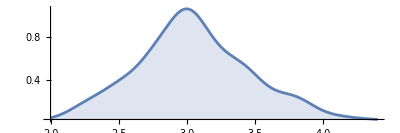
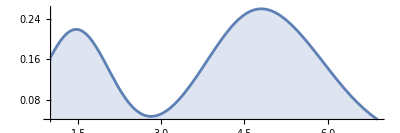
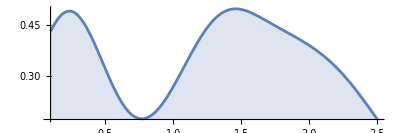

```mathematica
Plot[Evaluate@PDF[SmoothKernelDistribution[#],x],{x,Min[#],Max[#]},Filling->Axis,PlotRange->All,PlotTheme->"Minimal",AspectRatio->1/3]&/@{sepalLength,sepalWidth,petalLength,petalWidth}(*绘制概率密度估计曲线*)
```

## 散点图

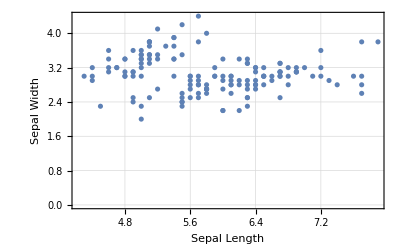

```mathematica
ListPlot[Table[irisData[[i,1,1;;2]],{i,1,150}],PlotTheme->"Detailed",FrameLabel->{"Sepal Length","Sepal Width"}]
```

```mathematica
ListPointPlot3D[Table[irisData[[i,1,1;;3]],{i,1,150}],PlotTheme->"Detailed",AxesLabel->{"Sepal Length","Sepal Width","Petal Length"}]
```

-Graphics3D-

## 余弦距离

```mathematica
cosineDistanceIris[m_,n_]:=Block[{a,b},{a,b}=Table[irisData[[i,1,1;;4]],{i,1,150}][[{m,n}]];CosineDistance[a,b]]
```

```mathematica
cosineDistanceIris[1,2]
```

0.00142084

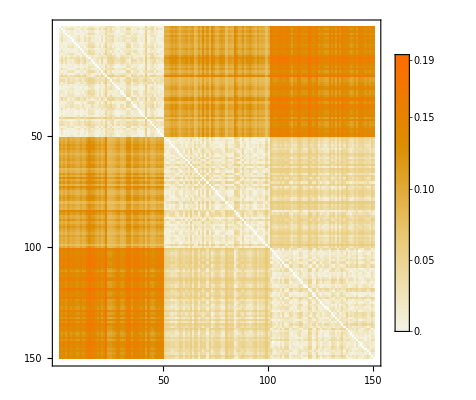

```mathematica
MatrixPlot[Table[cosineDistanceIris[i,j],{i,1,150},{j,1,150}],PlotTheme->"Detailed"](*同类之间颜色最浅，即余弦距离最近*)
```

## 张量积

```mathematica
String2Pic[string_]:=Rasterize[Text[string],RasterSize->100,ImageSize->50](*将符号转化为图片*)
TensorProductMatrixPlot[a_List,b_List]:=Module[{tp,plots},
tp=TensorProduct[a,b];
plots=MatrixPlot[#,PlotTheme->"Minimal"]&/@{Transpose[{a}],Transpose[{b}],tp};
GraphicsRow[{plots[[1]],String2Pic["⊗"],plots[[2]],String2Pic["="],plots[[3]]}]
]
```

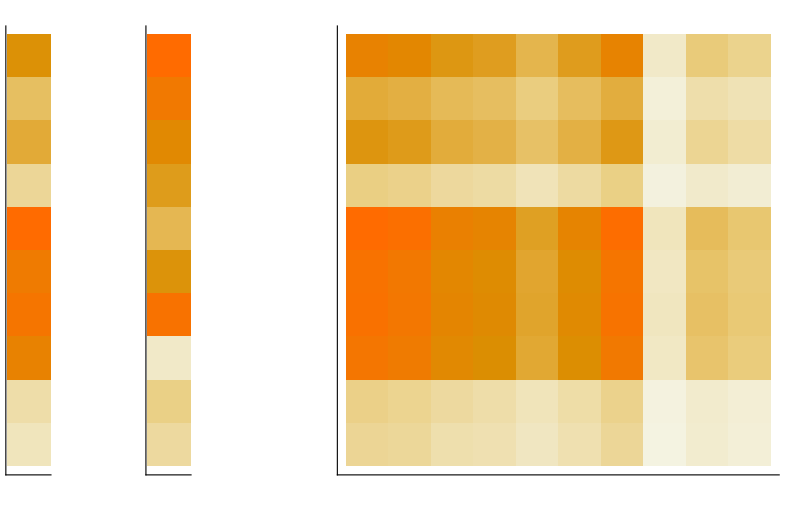

```mathematica
a=RandomReal[10,10];
b=RandomReal[10,10];
TensorProductMatrixPlot[a,b]
```

```mathematica
MatrixRank[tp] (*非零向量的张量积的秩为一*)
```

MatrixRank[tp]

## 向量范数

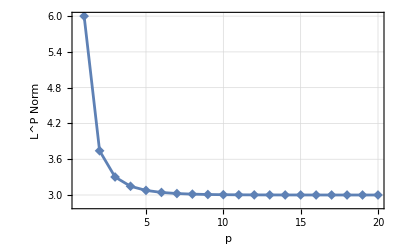

```mathematica
ListLinePlot[Table[Norm[{1,2,3},i],{i,1,20}],PlotMarkers->{"◆", 10},PlotTheme->"Detailed",FrameLabel->{"p","L^P Norm"},PlotRange->All]
```